```mathematica
induced Polarization in E-field of an isolated conductive sphere
```

```mathematica
in uniform E-field in Z direction
```

```mathematica
E=E z = E  Cos[θ]
```

```mathematica
the potential from this field is
```

```mathematica
ϕ=- E r Cos[θ]
```

```mathematica
in side the prefect conductive sphere, potential =0
```

```mathematica
Set the potential out side is
```

```mathematica
Ψ[r,θ]=∑_(l=0)^∞ (Subscript[A, l] r^l+Subscript[B, l]/r^(l+1))LegendreP[l,u=Cos[θ]]
```

```mathematica
since out side is no chrage, it is the lapacian equation
```

```mathematica
MatrixForm[Table[LegendreP[l,Cos[θ]],{l,0,7}]]
```

(1
Cos[θ]
1/2 (-1+3 Cos[θ]^2)
1/2 (-3 Cos[θ]+5 Cos[θ]^3)
1/8 (3-30 Cos[θ]^2+35 Cos[θ]^4)
1/8 (15 Cos[θ]-70 Cos[θ]^3+63 Cos[θ]^5)
1/16 (-5+105 Cos[θ]^2-315 Cos[θ]^4+231 Cos[θ]^6)
1/16 (-35 Cos[θ]+315 Cos[θ]^3-693 Cos[θ]^5+429 Cos[θ]^7))

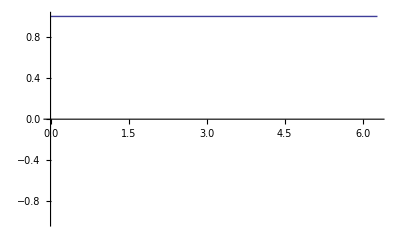
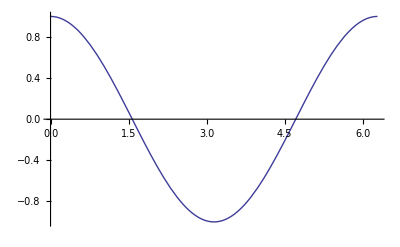
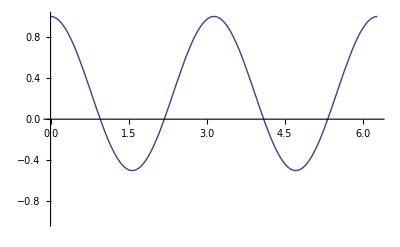
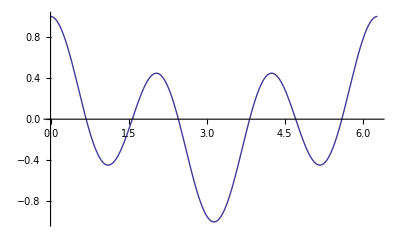
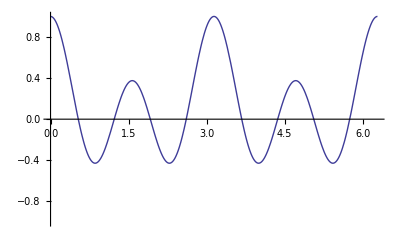
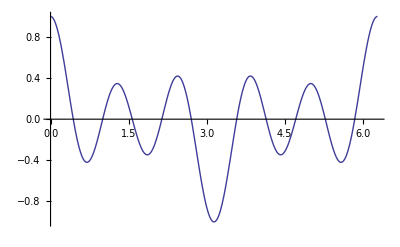
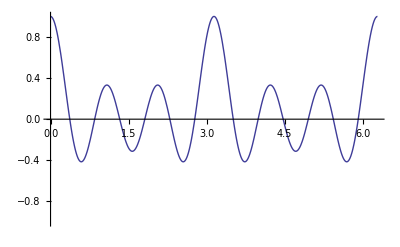
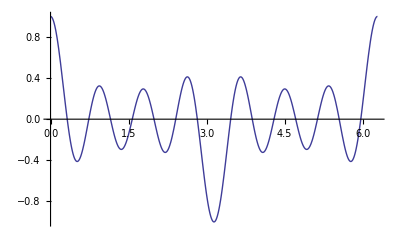

```mathematica
Table[Plot[LegendreP[l,Cos[θ]],{θ,0,2π},PlotRange->1],{l,0,7}]
```

```mathematica
Subscript[A, l]=0 since outside field needed to be convergence
```

```mathematica
Ψ[r,θ]=∑_(l=0)^∞ Subscript[B, l]/r^(l+1)LegendreP[l,u=Cos[θ]]
```

```mathematica
the BC is continoun of the field
```

```mathematica
n.(Subscript[D, out]-Subscript[D, in])=σ
-> ϵ Subscript[E, out.n]=σ
n×(Subscript[E, out]-Subscript[E, in])=0
n= {Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ], Cos[θ]}
```

```mathematica
Assume the shpere is Potential zero
```

```mathematica
Φ[a,θ]=0=∑_(l=0)^∞ Subscript[B, l]/a^(l+1)LegendreP[l,u=Cos[θ]]-E a Cos[θ]
```

```mathematica
in order to be equal
```

```mathematica
Subscript[B, 1] is not zero, Subscript[B, i] are all Zero
```

```mathematica
Subscript[B, 1]/a^2 Cos[θ]-E a Cos[θ]=0
Subscript[B, 1]=E a^3
```

```mathematica
Ψ[r,θ]=(E a^3)/r^2 Cos[θ]-E r Cos[θ] = E Cos[θ] (a^3/r^2-r)
```

```mathematica
Plot Potential
```

field for the uniform

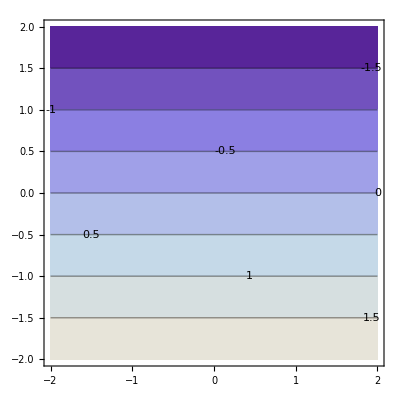

```mathematica
for the uniform field
ContourPlot[ -z, {x,-2,2},{z,-2,2},ContourLabels->Automatic]
```

```mathematica
Ψ[r,θ,ϕ]-> Ψ[x,y,z]
```

```mathematica
Cos[θ] (a/r^2-r)/.{r-> √(x^2+y^2+z^2),Cos[θ]->z/(√(x^2+y^2+z^2))}
```

(z (a/(x^2+y^2+z^2)-√(x^2+y^2+z^2)))/(√(x^2+y^2+z^2))

```mathematica
z (-1+a/((x^2+y^2+z^2)^(3/2)))/.y->0
```

z (-1+a/((x^2+z^2)^(3/2)))

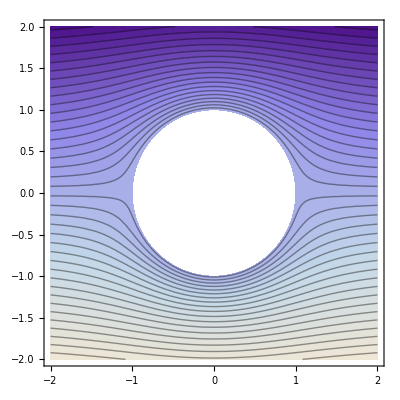

```mathematica
ContourPlot[z (-1+1/((x^2+z^2)^(3/2))),{x,-2,2},{z,-2,2},RegionFunction->Function[{x,z},1<x^2+z^2],Contours->Function[{min,max},Range[min,max,0.1]]]
```

```mathematica
Plot3D[z (-1+1/((x^2+z^2)^(3/2))),{x,-2,2},{z,-2,2},RegionFunction->Function[{x,z},1<x^2+z^2]]
```

-Graphics3D-

```mathematica
Manipulate[Plot[z (-1+1/((x^2+z^2)^(3/2))),{x,-2,2},AspectRatio->Automatic],{z,-2,2}]
```

```mathematica
Plot Field Line (Potential Flow)
```

```mathematica
du=Subscript[u, x] dx+Subscript[u, z] dz
du=0
dz/dx=(-Subscript[u, x])/Subscript[u, z]
```

```mathematica
so, the perpendicular line
dz/dx=Subscript[u, z]/Subscript[u, x]
```

```mathematica
Solve[z (-1+1/((x^2+z^2)^(3/2)))==k,x]
```

{{x→-√(-z^2+(z ((k+z)/z)^(1/3))/(k+z))},{x→√(-z^2+(z ((k+z)/z)^(1/3))/(k+z))}}

```mathematica
Manipulate[Plot[√(-z^2+(z ((k+z)/z)^(1/3))/(k+z)),{z,-2,2},AspectRatio->Automatic],{k,-1,1}]
```

```mathematica
D[z (-1+1/((x^2+z^2)^(3/2))),z]
```

-1-(3 z^2)/((x^2+z^2)^(5/2))+1/((x^2+z^2)^(3/2))

```mathematica
Manipulate[Plot[-1-(3 z^2)/((x^2+z^2)^(5/2))+1/((x^2+z^2)^(3/2)),{z,-2,2},AspectRatio->Automatic],{x,-2,2}]
```

```mathematica
D[z (-1+1/((x^2+z^2)^(3/2))),x]/D[z (-1+1/((x^2+z^2)^(3/2))),z]
```

```mathematica
-(3 x z)/((x^2+z^2)^(5/2) (-1-(3 z^2)/((x^2+z^2)^(5/2))+1/((x^2+z^2)^(3/2))))/.z->z[x]
```

```mathematica
DSolve[z'[x]==-(3 x z[x])/((x^2+z[x]^2)^(5/2) (-1-(3 z[x]^2)/((x^2+z[x]^2)^(5/2))+1/((x^2+z[x]^2)^(3/2)))),z[x],x]
```

DSolve[z'[x]==-(3 x z[x])/((x^2+z[x]^2)^(5/2) (-1-(3 z[x]^2)/((x^2+z[x]^2)^(5/2))+1/((x^2+z[x]^2)^(3/2)))),z[x],x]

```mathematica
Plot3D[-(3 x z)/((x^2+z^2)^(5/2) (-1-(3 z^2)/((x^2+z^2)^(5/2))+1/((x^2+z^2)^(3/2)))),{x,-2,2},{z,-2,2}]
```

-Graphics3D-

```mathematica
******************************************************************************
```

```mathematica
The Potential for Zero Potential unit Sphere
```

```mathematica
Ψ[r,θ]= Cos[θ] (1/r^2-r)
```

```mathematica
Needs["VectorAnalysis`"]
```

```mathematica
SetCoordinates[Spherical[r,θ,ϕ]]
```

Spherical[r,θ,ϕ]

```mathematica
Grad[Cos[θ] (1/r^2-r)]
```

{(-1-2/r^3) Cos[θ],-((1/r^2-r) Sin[θ])/r,0}

```mathematica
Subscript[E, r]=(-1-2/r^3) Cos[θ]
```

```mathematica
Subscript[E, θ]=-((1/r^2-r) Sin[θ])/r
```

```mathematica
the BC of tangential component is automatic fullfill
```

```mathematica
the Surfacr Charge is
```

```mathematica
σ=-3ϵ Cos[θ]
```

```mathematica
the Polarization
P=z σ = -3ϵ Cos[θ] z
```

```mathematica
the effective ϵ
```

```mathematica
CoordinatesToCartesian[{(-1-2/r^3) Cos[θ],-((1/r^2-r) Sin[θ])/r,0}, Spherical[r,θ,ϕ]]
```

{-(-1-2/r^3) Cos[θ] Sin[((1/r^2-r) Sin[θ])/r],0,(-1-2/r^3) Cos[θ] Cos[((1/r^2-r) Sin[θ])/r]}

```mathematica
Needs["VectorFieldPlots`"]
```

Power::infy: Infinite expression 1/0^5/2 encountered.

∞::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0^5/2 encountered.

∞::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0^3/2 encountered.

General::stop: Further output of Power :: "infy" will be suppressed during this calculation.

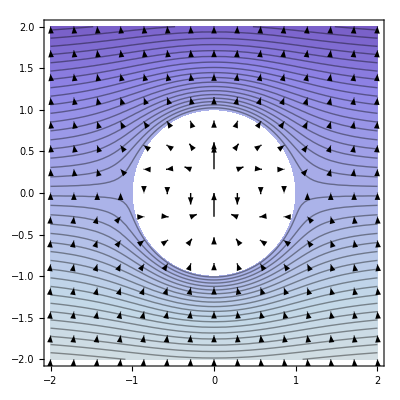

```mathematica
Show[
ContourPlot[z (-1+1/((x^2+z^2)^(3/2))),{x,-2,2},{z,-2,2},RegionFunction->Function[{x,z},1<x^2+z^2],Contours->Function[{min,max},Range[min,max,0.1]]],

GradientFieldPlot[-z (-1+1/((x^2+z^2)^(3/2))), {x, -2, 2}, {z, -2, 2}]
]
```